# Reciprocal Multifactorial Constants

## Perfect matchings for K_ 6 and K_8

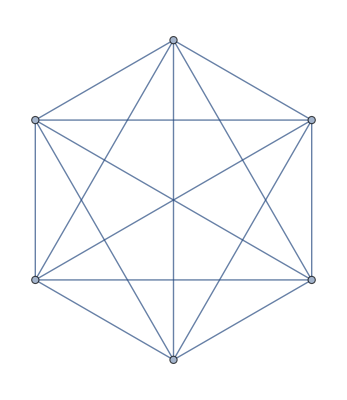

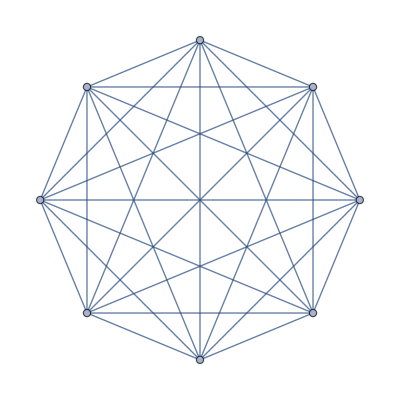

```mathematica
k6=CompleteGraph[6]
k8=CompleteGraph[8]
```

```mathematica
l6=Length[FindIndependentEdgeSet[k6]]
l8=Length[FindIndependentEdgeSet[k8]]
```

3

4

```mathematica
esl6=Select[Subsets[EdgeList[k6],{l6}],IndependentEdgeSetQ[k6,#]&]
esl8=Select[Subsets[EdgeList[k8],{l8}],IndependentEdgeSetQ[k8,#]&]
```

{{1<->2,3<->4,5<->6},{1<->2,3<->5,4<->6},{1<->2,3<->6,4<->5},{1<->3,2<->4,5<->6},{1<->3,2<->5,4<->6},{1<->3,2<->6,4<->5},{1<->4,2<->3,5<->6},{1<->4,2<->5,3<->6},{1<->4,2<->6,3<->5},{1<->5,2<->3,4<->6},{1<->5,2<->4,3<->6},{1<->5,2<->6,3<->4},{1<->6,2<->3,4<->5},{1<->6,2<->4,3<->5},{1<->6,2<->5,3<->4}}

{{1<->2,3<->4,5<->6,7<->8},{1<->2,3<->4,5<->7,6<->8},{1<->2,3<->4,5<->8,6<->7},{1<->2,3<->5,4<->6,7<->8},{1<->2,3<->5,4<->7,6<->8},{1<->2,3<->5,4<->8,6<->7},{1<->2,3<->6,4<->5,7<->8},{1<->2,3<->6,4<->7,5<->8},{1<->2,3<->6,4<->8,5<->7},{1<->2,3<->7,4<->5,6<->8},{1<->2,3<->7,4<->6,5<->8},{1<->2,3<->7,4<->8,5<->6},{1<->2,3<->8,4<->5,6<->7},{1<->2,3<->8,4<->6,5<->7},{1<->2,3<->8,4<->7,5<->6},{1<->3,2<->4,5<->6,7<->8},{1<->3,2<->4,5<->7,6<->8},{1<->3,2<->4,5<->8,6<->7},{1<->3,2<->5,4<->6,7<->8},{1<->3,2<->5,4<->7,6<->8},{1<->3,2<->5,4<->8,6<->7},{1<->3,2<->6,4<->5,7<->8},{1<->3,2<->6,4<->7,5<->8},{1<->3,2<->6,4<->8,5<->7},{1<->3,2<->7,4<->5,6<->8},{1<->3,2<->7,4<->6,5<->8},{1<->3,2<->7,4<->8,5<->6},{1<->3,2<->8,4<->5,6<->7},{1<->3,2<->8,4<->6,5<->7},{1<->3,2<->8,4<->7,5<->6},{1<->4,2<->3,5<->6,7<->8},{1<->4,2<->3,5<->7,6<->8},{1<->4,2<->3,5<->8,6<->7},{1<->4,2<->5,3<->6,7<->8},{1<->4,2<->5,3<->7,6<->8},{1<->4,2<->5,3<->8,6<->7},{1<->4,2<->6,3<->5,7<->8},{1<->4,2<->6,3<->7,5<->8},{1<->4,2<->6,3<->8,5<->7},{1<->4,2<->7,3<->5,6<->8},{1<->4,2<->7,3<->6,5<->8},{1<->4,2<->7,3<->8,5<->6},{1<->4,2<->8,3<->5,6<->7},{1<->4,2<->8,3<->6,5<->7},{1<->4,2<->8,3<->7,5<->6},{1<->5,2<->3,4<->6,7<->8},{1<->5,2<->3,4<->7,6<->8},{1<->5,2<->3,4<->8,6<->7},{1<->5,2<->4,3<->6,7<->8},{1<->5,2<->4,3<->7,6<->8},{1<->5,2<->4,3<->8,6<->7},{1<->5,2<->6,3<->4,7<->8},{1<->5,2<->6,3<->7,4<->8},{1<->5,2<->6,3<->8,4<->7},{1<->5,2<->7,3<->4,6<->8},{1<->5,2<->7,3<->6,4<->8},{1<->5,2<->7,3<->8,4<->6},{1<->5,2<->8,3<->4,6<->7},{1<->5,2<->8,3<->6,4<->7},{1<->5,2<->8,3<->7,4<->6},{1<->6,2<->3,4<->5,7<->8},{1<->6,2<->3,4<->7,5<->8},{1<->6,2<->3,4<->8,5<->7},{1<->6,2<->4,3<->5,7<->8},{1<->6,2<->4,3<->7,5<->8},{1<->6,2<->4,3<->8,5<->7},{1<->6,2<->5,3<->4,7<->8},{1<->6,2<->5,3<->7,4<->8},{1<->6,2<->5,3<->8,4<->7},{1<->6,2<->7,3<->4,5<->8},{1<->6,2<->7,3<->5,4<->8},{1<->6,2<->7,3<->8,4<->5},{1<->6,2<->8,3<->4,5<->7},{1<->6,2<->8,3<->5,4<->7},{1<->6,2<->8,3<->7,4<->5},{1<->7,2<->3,4<->5,6<->8},{1<->7,2<->3,4<->6,5<->8},{1<->7,2<->3,4<->8,5<->6},{1<->7,2<->4,3<->5,6<->8},{1<->7,2<->4,3<->6,5<->8},{1<->7,2<->4,3<->8,5<->6},{1<->7,2<->5,3<->4,6<->8},{1<->7,2<->5,3<->6,4<->8},{1<->7,2<->5,3<->8,4<->6},{1<->7,2<->6,3<->4,5<->8},{1<->7,2<->6,3<->5,4<->8},{1<->7,2<->6,3<->8,4<->5},{1<->7,2<->8,3<->4,5<->6},{1<->7,2<->8,3<->5,4<->6},{1<->7,2<->8,3<->6,4<->5},{1<->8,2<->3,4<->5,6<->7},{1<->8,2<->3,4<->6,5<->7},{1<->8,2<->3,4<->7,5<->6},{1<->8,2<->4,3<->5,6<->7},{1<->8,2<->4,3<->6,5<->7},{1<->8,2<->4,3<->7,5<->6},{1<->8,2<->5,3<->4,6<->7},{1<->8,2<->5,3<->6,4<->7},{1<->8,2<->5,3<->7,4<->6},{1<->8,2<->6,3<->4,5<->7},{1<->8,2<->6,3<->5,4<->7},{1<->8,2<->6,3<->7,4<->5},{1<->8,2<->7,3<->4,5<->6},{1<->8,2<->7,3<->5,4<->6},{1<->8,2<->7,3<->6,4<->5}}

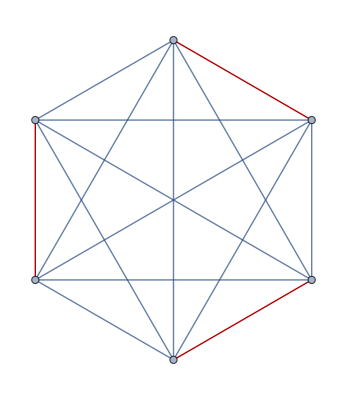
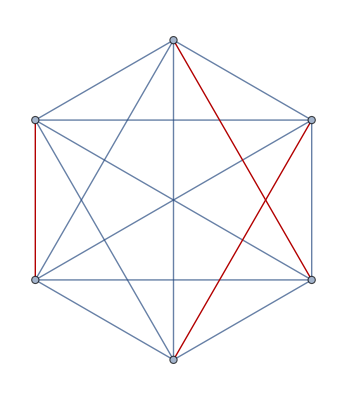
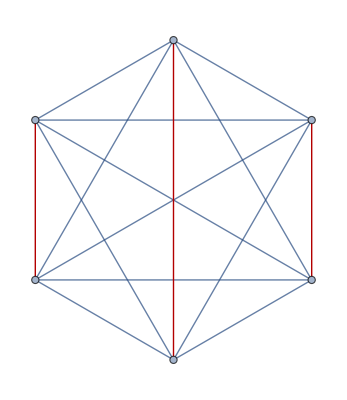
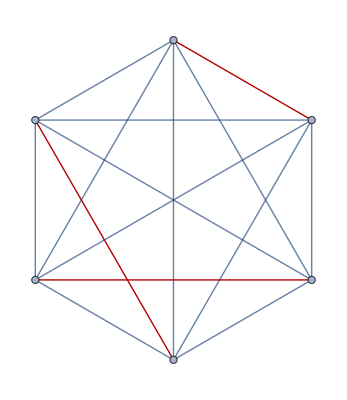
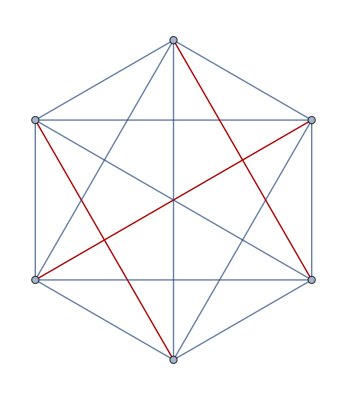
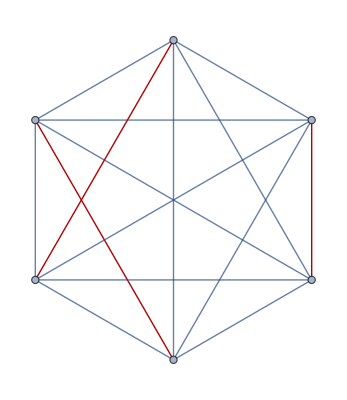
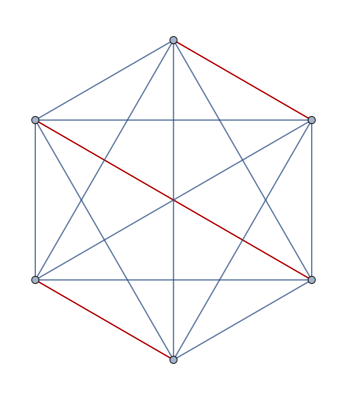
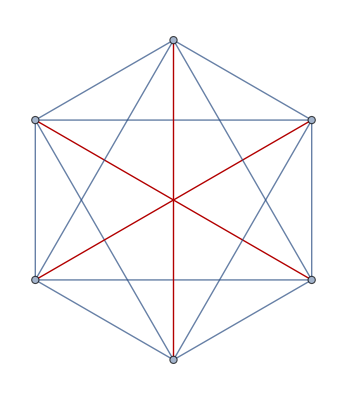

```mathematica
Table[HighlightGraph[k6,h,GraphHighlightStyle->"Thick"],{h,esl6}]
```

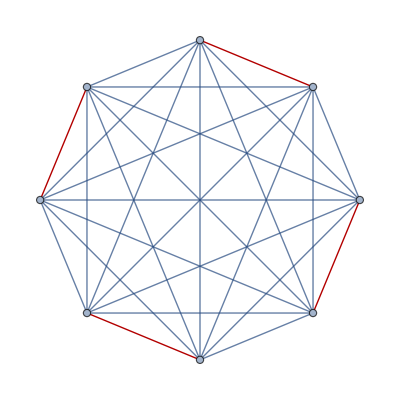
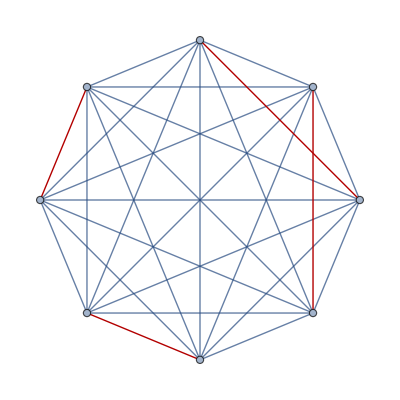
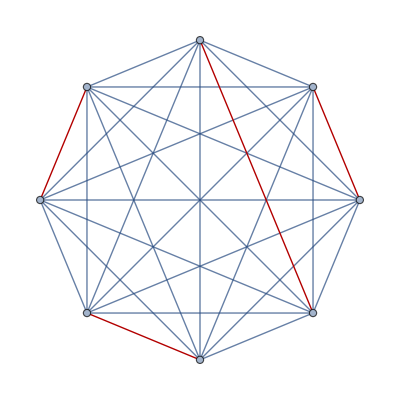
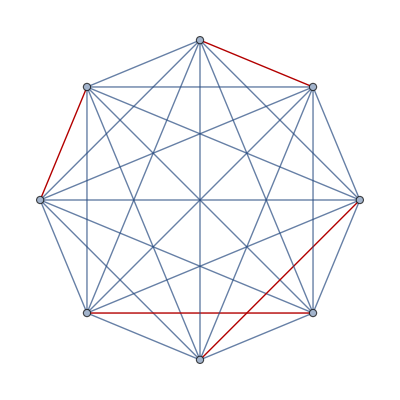
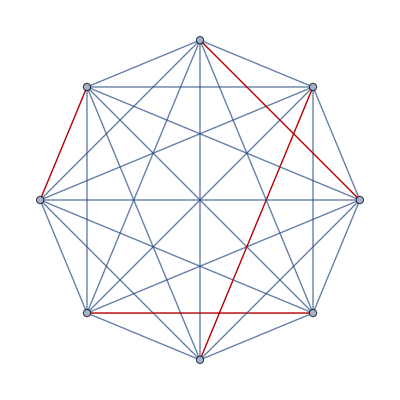
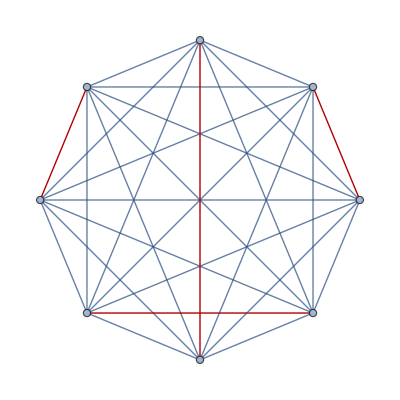
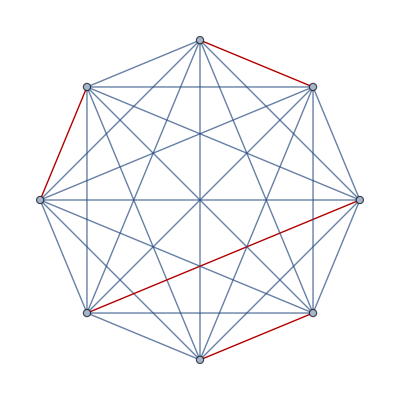
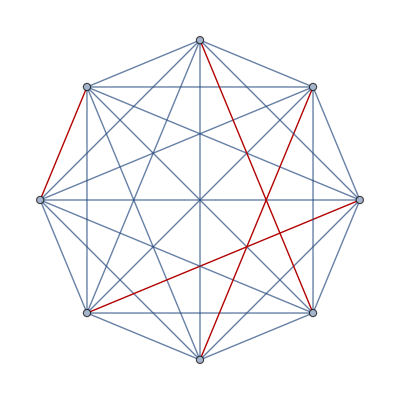

```mathematica
Table[HighlightGraph[k8,h,GraphHighlightStyle->"Thick"],{h,esl8}]
```

## Stirling Permutations

```mathematica
stirlingPermutation[k_]:=(list=Riffle[Table[i,{i,1,k}],Table[i,{i,1,k}]];
check[x_List]:=(done={};
n=1;
While[n≤Length[x],If[MemberQ[done,x[[n]]],p=Position[done,x[[n]]][[1]][[1]];
If[Min[done[[p;;]]]≠x[[n]],Return[False]]];
AppendTo[done,x[[n]]];
n++;];
Return[True];);
Multicolumn[Select[Permutations[list],check[#]&],k])
```

```mathematica
stirlingPermutation[4]
```

{1,1,2,2,3,3,4,4} | {1,2,4,4,2,1,3,3} | {2,2,1,4,4,1,3,3} | {3,3,2,2,1,4,4,1}
{1,1,2,2,3,4,4,3} | {1,2,4,4,2,3,3,1} | {2,2,1,4,4,3,3,1} | {3,3,2,2,4,4,1,1}
{1,1,2,2,4,4,3,3} | {1,2,4,4,3,3,2,1} | {2,2,3,3,1,1,4,4} | {3,3,2,4,4,2,1,1}
{1,1,2,3,3,2,4,4} | {1,3,3,1,2,2,4,4} | {2,2,3,3,1,4,4,1} | {3,3,4,4,1,1,2,2}
{1,1,2,3,3,4,4,2} | {1,3,3,1,2,4,4,2} | {2,2,3,3,4,4,1,1} | {3,3,4,4,1,2,2,1}
{1,1,2,3,4,4,3,2} | {1,3,3,1,4,4,2,2} | {2,2,3,4,4,3,1,1} | {3,3,4,4,2,2,1,1}
{1,1,2,4,4,2,3,3} | {1,3,3,2,2,1,4,4} | {2,2,4,4,1,1,3,3} | {3,4,4,3,1,1,2,2}
{1,1,2,4,4,3,3,2} | {1,3,3,2,2,4,4,1} | {2,2,4,4,1,3,3,1} | {3,4,4,3,1,2,2,1}
{1,1,3,3,2,2,4,4} | {1,3,3,2,4,4,2,1} | {2,2,4,4,3,3,1,1} | {3,4,4,3,2,2,1,1}
{1,1,3,3,2,4,4,2} | {1,3,3,4,4,1,2,2} | {2,3,3,2,1,1,4,4} | {4,4,1,1,2,2,3,3}
{1,1,3,3,4,4,2,2} | {1,3,3,4,4,2,2,1} | {2,3,3,2,1,4,4,1} | {4,4,1,1,2,3,3,2}
{1,1,3,4,4,3,2,2} | {1,3,4,4,3,1,2,2} | {2,3,3,2,4,4,1,1} | {4,4,1,1,3,3,2,2}
{1,1,4,4,2,2,3,3} | {1,3,4,4,3,2,2,1} | {2,3,3,4,4,2,1,1} | {4,4,1,2,2,1,3,3}
{1,1,4,4,2,3,3,2} | {1,4,4,1,2,2,3,3} | {2,3,4,4,3,2,1,1} | {4,4,1,2,2,3,3,1}
{1,1,4,4,3,3,2,2} | {1,4,4,1,2,3,3,2} | {2,4,4,2,1,1,3,3} | {4,4,1,2,3,3,2,1}
{1,2,2,1,3,3,4,4} | {1,4,4,1,3,3,2,2} | {2,4,4,2,1,3,3,1} | {4,4,1,3,3,1,2,2}
{1,2,2,1,3,4,4,3} | {1,4,4,2,2,1,3,3} | {2,4,4,2,3,3,1,1} | {4,4,1,3,3,2,2,1}
{1,2,2,1,4,4,3,3} | {1,4,4,2,2,3,3,1} | {2,4,4,3,3,2,1,1} | {4,4,2,2,1,1,3,3}
{1,2,2,3,3,1,4,4} | {1,4,4,2,3,3,2,1} | {3,3,1,1,2,2,4,4} | {4,4,2,2,1,3,3,1}
{1,2,2,3,3,4,4,1} | {1,4,4,3,3,1,2,2} | {3,3,1,1,2,4,4,2} | {4,4,2,2,3,3,1,1}
{1,2,2,3,4,4,3,1} | {1,4,4,3,3,2,2,1} | {3,3,1,1,4,4,2,2} | {4,4,2,3,3,2,1,1}
{1,2,2,4,4,1,3,3} | {2,2,1,1,3,3,4,4} | {3,3,1,2,2,1,4,4} | {4,4,3,3,1,1,2,2}
{1,2,2,4,4,3,3,1} | {2,2,1,1,3,4,4,3} | {3,3,1,2,2,4,4,1} | {4,4,3,3,1,2,2,1}
{1,2,3,3,2,1,4,4} | {2,2,1,1,4,4,3,3} | {3,3,1,2,4,4,2,1} | {4,4,3,3,2,2,1,1}
{1,2,3,3,2,4,4,1} | {2,2,1,3,3,1,4,4} | {3,3,1,4,4,1,2,2} | 
{1,2,3,3,4,4,2,1} | {2,2,1,3,3,4,4,1} | {3,3,1,4,4,2,2,1} | 
{1,2,3,4,4,3,2,1} | {2,2,1,3,4,4,3,1} | {3,3,2,2,1,1,4,4} |

## Limits for Ratio test in m(2)

```mathematica
limitm2case1=Limit[(2^(1+2 n) n! (1+n)!)/(2 (1+n))!,n->Infinity]
limitm2case2=Limit[(2^(-1-2 n) (2 n)!)/(n! (1+n)!),n->Infinity]
```

0

0

## Computing m(1) to m(10) from n=0 to n=2000

```mathematica
Multifactorial[n_,k_]:=Abs[Apply[Times,Range[-n,-1,k]]]
```

```mathematica
For[i=1,i<11, i++, Print[N[Sum[1/Multifactorial[n,i],{n,0,2000}], 10]]]
```

2.718281828

3.059407405

3.298913538

3.485944977

3.640224468

3.771902396

3.886959654

3.989241213

4.08137552

4.165243766

## Plot of m (1) to m (1) superimposed on each other from n = 0 to n = 2000

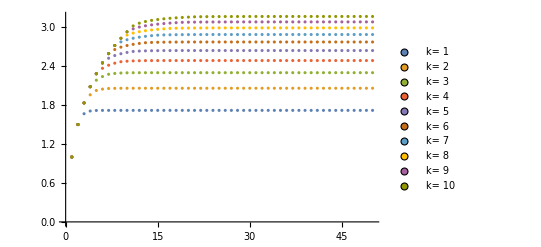

```mathematica
ListPlot[Table[Sum[1/Multifactorial[n,j],{n,1,i}],{j,1,10},{i,1,20}],PlotLegends->PointLegend[Automatic,PromptForm[k,#]&/@Range[10],LegendMarkers->{Graphics[Disk[]],6}]]
```

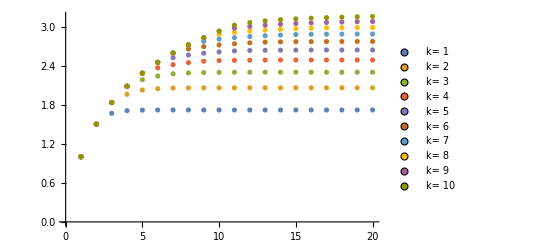

```mathematica
ListPlot[Table[Sum[1/Multifactorial[n,j],{n,1,i}],{j,1,10},{i,1,50}],PlotLegends->PointLegend[Automatic,PromptForm[k,#]&/@Range[10],LegendMarkers->{Graphics[Disk[]],6}]]
```